# IoT: Intel Edison & Arduino IDE

Warning: Make sure connection to the Edison on Mathematica is closed before uploading anything via the Arduino IDE, or clicking the Serial Monitor button. Not doing this may halt the Arduino IDE.

Connect to Intel Edison

```mathematica
edison = DeviceOpen["Serial",{"/dev/tty.usbmodem1413","BaudRate"->115200}];
```

Create an empty list in which data will be collected. (See Data bin section, a more interesting way of collecting the data!)

## Visualising Data

```mathematica
data={};
```

Create & run a scheduled task that will add new data to the list, every second.

```mathematica
task1=RunScheduledTask[
Block[{csv,raw},
csv=FromCharacterCode[DeviceReadBuffer[edison]]; (* convert from ASCII to normal characters *)
raw=ImportString[csv,"List"];
data=Join[data,raw];
],1];
```

Visualise temperature data for the last 60 seconds. I’m using 60s so as to reduce the time it takes to generate a new plot.

```mathematica
With[
{
col=Brown(* overall theme & text colour *)
},

Column[{
(* display date, time and temperature *)
Column[{
Dynamic[Style[DateString[{"Hour12",".","Minute",".","Second"," ","AMPM"," | ","DayNameShort"," ","Day"," ","MonthNameShort"}],Darker@col],UpdateInterval->1],
Dynamic[Framed[Quantity[Last@data,"DegreesCelsius"],FrameStyle->col],UpdateInterval->1]
},Alignment->Center,Spacings->1.],

(* show a plot of temperature for the last 1 minute & thermometer *)
Row[{
Dynamic[ListLinePlot[data⟦-60;;⟧,Filling->Axis,FillingStyle->Lighter[col,.95],PlotStyle->{Thickness[0.001],Darker@col},PlotRange->All,AxesLabel->{"seconds ago","°C"},ImageSize->400],UpdateInterval->1],
Dynamic[ThermometerGauge[Quantity[Last@data,"DegreesCelsius"],{0,100},PerformanceGoal->"Speed"],UpdateInterval->1]
}]
},Dividers->Center,FrameStyle->Darker@col,Alignment->Center,Spacings->2]
]
```

Remember that we’re adding a new entry to the data every second, so this list will grow quickly. But memory-wise, the size of data should remain manageably small for playing around and trying things out; 2500 entries only amount to about 60 Kb.

## Using Data Drop

Instead of throwing everything into data, we can collect the temperature readings in a different way, using the . This way we can access, manipulate, and even add new entries the our databin - from wherever, at anytime - in so many different ways including email and Twitter. We can swiftly gain insight into our data via Wolfram Alpha. You can create a new databin either in Mathematica or online. Either way, you’ll receive a short ID with which you can access it. For this section, I edited the Arduino code to send the data the serial port every 5 seconds, rather than every second as before.

Let' s create a new databin name TempDataBin, which stores temperature readings entered as temp.

```mathematica
TempDataBin=CreateDatabin[{
"Name"->"TempDataBin",
"Interpretation"->"temp"->Restricted["StructuredQuantity","DegreesCelsius"]
}]
```

Our databin short ID is 6FuSuRRs, and since this databin was created using a free account, it is only temporary and will expire a month from now. Let’s go ahead and a add an entry to it -- the most recent value stored in data.

```mathematica
DatabinAdd[TempDataBin,<|"temp"->data⟦-1⟧|>]
```

And view what we’ve just added.

```mathematica
Databin[TempDataBin,-1]//Values
```

<|temp→{8.02 °C}|>

As you can see, our entry was automatically stored as a temperature reading, because when we created the databin we defined all values entered as temp as such. 

Now we can go ahead and continuously store new data in this bin. To do this, we’ll stop task1, and modify it to add to the bin as new data comes in.

```mathematica
StopScheduledTask/@ScheduledTasks[];
RemoveScheduledTask/@ScheduledTasks[];
```

```mathematica
data2={};
```

```mathematica
task2=RunScheduledTask[
Block[{csv,raw},
csv=FromCharacterCode[DeviceReadBuffer[edison]];
raw=ImportString[csv,"List"];
data2=Join[data2,raw];
DatabinAdd[TempDataBin,<|"temp"->data2⟦-1⟧|>];
],7.5]
```

Similar to task1, task2 will add new data (the last value stored in data2) to our bin every 7.5 seconds, half way inbetween when that value was stored in data2 and when the next one will be.

After 60 entries have been added to the bin, an error occurs: normal rate of 60 entries per hour exceeded. I assume this limitation only holds for a free account, but one can adjust the rate of adding new data to a bin to overcome this. 

Anyway, let’s view the entries that have been stored so far.

```mathematica
Databin["6FuSuRRs"]
```

```mathematica
TimeSeries[TempDataBin]
```

<|temp→TimeSeries[…]|>

```mathematica
Values[TempDataBin]
```

<|temp→{8.02 °C,8.02 °C,7.93 °C,7.83 °C,8.11 °C,8.02 °C,8.02 °C,7.74 °C,8.11 °C,7.83 °C,8.02 °C,8.02 °C,7.83 °C,7.93 °C,8.11 °C,7.83 °C,7.83 °C,7.83 °C,7.83 °C,8.02 °C,7.93 °C,8.02 °C,8.02 °C,7.83 °C,8.02 °C,7.93 °C,7.93 °C,7.93 °C,7.93 °C,7.93 °C,8.02 °C,8.02 °C,7.93 °C,8.11 °C,8.11 °C,7.74 °C,8.02 °C,8.02 °C,8.02 °C,8.02 °C,8.2 °C,7.83 °C,8.02 °C,7.93 °C,7.83 °C,8.02 °C,8.11 °C,7.93 °C,7.93 °C,7.93 °C,8.11 °C,8.11 °C,8.11 °C,8.02 °C,8.02 °C,8.02 °C,8.02 °C,7.93 °C,7.93 °C,7.83 °C}|>

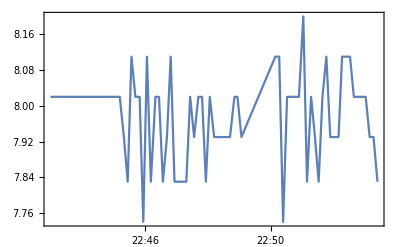
<|temp→-Graphics-|>

```mathematica
DateListPlot[TempDataBin]
```

We can also view this in great detail in Wolfram Alpha.

```mathematica
WolframAlpha["databin 6FuSuRRs"]
```

WolframAlphaQueryResults

Disconnect the Edison.

```mathematica
DeviceClose[edison];
Quit[];
```